# CLITools

A collection of command line tools and utilities, streamlining WolframScript creation

## Definition

### Testing

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "CLITools.wl"}]];
```

### Release

```mathematica
Block[{ cellData = Import[FileNameJoin[{NotebookDirectory[], "CLITools.wl"}], "Text"] },
	NotebookLocate["Code_Definition"];
	NotebookDelete[];
	cellData = StringDelete[cellData,"(*--" | "--*)" ];
	CellPrint[Cell[TextData@"Code", "Subsubsection", CellTags->{ "Code_Definition" }]];
	CellPrint[Cell[BoxData@cellData, "Input", CellTags->{ "Code_Definition" }]];
]
```

#### Code

```mathematica
(* ::Section:: *)(* Patterns *)
stringFormP = (_String|_StringExpression|_RegularExpression|_Alternatives|_Repeated);

argvP = HoldPattern[<|(_String -> _)... |>];

cliInterfaceCommandsP = KeyValuePattern[{(stringFormP :> expr_)...}] | <||>;

inputCommandP = { __String } | _String;

logTypeP = "INFO"|"ERROR"|"SUCCESS"|"WARN";

optionLongP = _String?(StringStartsQ["--"]);
optionShortP = _String?(StringStartsQ["-"]);
optionsP = optionLongP | optionShortP;

argumentSpecP = HoldPattern[{
	Alternatives[
		(name_String | {longName_String, shortName_String}),
		(name_String | {longName_String, shortName_String}) -> Except[_Rule],
		(name_String | {longName_String, shortName_String}) -> pattern_ -> default_
	]...
}];


(* ::Section:: *)(* Utilities *)
validateOptions[o: OptionsPattern[CLITools]] := Module[{
		opts = <|o|>,
		pairs = {
			{"CommandLine",            inputCommandP},
			{"InterfacePrompt",        _String},
			{"OptionDelimiter",        _String},
			{"HelpMessage",            _String},
			{"LogToFile",              _String},
			{"LogToStdOut",            _String},
			{"LogDirectory",           _String},
			{"ArgumentDelimiter",      _String},
			{"ArgumentSpecification",  None | argumentSpecP},
			{"InterfaceCommands",      <|(_ :> _ )...|> }
		}
	},
	Enclose[
		Function[{name, pattern},
			If[KeyExistsQ[opts, name],
				ConfirmMatch[
					opts[name],
					pattern,
					"Invalid \"" <> name <> "\" option"
				]
			]
		] @@@ pairs;
		Success["options-validate-success", <||>]
	]
];

(* ::Section:: *)(* Options *)
CLITools // Options = {
	"CommandLine" -> Automatic,
	"InterfacePrompt" -> "wls-cli>",
	"InterfaceCommands" -> <|
		{("help" | "h" | "?"), "Show this help message"} :> Print[helpMessage],
		{("exit" | "quit" | "q"), "Exit the interface"} :> (
			shouldExit = True
		),
		{("eval" | "e"), "Evaluate Wolfram Language expression"} :> (
			With[{
					inLbl = StringTemplate["In[``]:= "][$Line],
					outLbl = StringTemplate["Out[``]:= "][$Line]
				},
				Print[outLbl, Input[inLbl]];
				$Line += 1;
			]
		)
	|>,
	"POSIX" -> False,
	"OptionDelimiter" -> (" " | "="),
	"ArgumentDelimiter" -> ",",
	"HelpMessage" -> "CLITools example interface",
	"LogToFile" -> True,
	"LogToStdOut" -> True,
	"LogDirectory" -> "./logs/wls-cli",
	"ArgumentSpecification" -> None,
	"StrictParse" -> False
};

(* ::Section:: *)(* Methods *)
(* ::Subsection:: *)(* Parse *)
(* ::Subsubsection:: *)(* Utilities *)
selectArgDefault[spec_, flag_String] := With[{res = selectArg[spec, flag]},
	Switch[res,
		(_String | {_String, _String}),
			False,
		Rule[_String | {_String, _String}, Except[_Rule]],
			Missing["NoDefault"],
		Rule[_String | {_String, _String}, _Rule],
			res[[2, 2]],
		_Missing,
			False,
		_,
			$Failed
	]
];

selectArgPattern[spec_, flag_String] := With[{
		res = selectArg[spec, flag]
	},
	Switch[res,
		(_String | {_String, _String}),
			_?BooleanQ,
		Rule[_String, Except[_Rule]],
			res[[2]],
		Rule[_String, _Rule],
			res[[2, 1]],
		Rule[{_String, _String}, Except[_Rule]],
			res[[2]],
		Rule[{_String, _String}, _Rule],
			res[[2, 1]],
		_,
			$Failed
	]
];

shortFlagMemberQ[spec_, flag_String] :=
	MemberQ[ getShortFlags @ spec, flag];

longFlagMemberQ[spec_, flag_String] :=
	MemberQ[ getLongFlags @ spec, flag];

flagMemberQ[spec_, flag_String] :=
	MemberQ[ getAllFlags @ spec, flag];

getLongFlags[ spec_ ] :=
	Flatten @ Map[
		Function @ Switch[#,
			_String,
				#,
			{_String, _String},
				#[[1]],
			Rule[_String, _],
				#[[1]],
			Rule[{_String, _String}, _],
				#[[1, 1]],
			_,
				Nothing
		],
		spec
	];

getShortFlags[ spec_ ] :=
	Map[
		Function @ Switch[#,
			{_String, _String},
				#[[2]],
			Rule[{_String, _String},_],
				#[[1,2]],
			_,
				Nothing
		],
		spec
	];

getAllFlags[ spec_ ] :=
	Flatten @ Map[
		Function @ Switch[#,
			_String | {_String, _String},
				{#},
			Rule[_String | {_String, _String}, _],
				{#[[1]]},
			_,
				Nothing
		],
		spec
	];

selectArg[ spec_, name_String ] := With[{
		form = StringDelete[name, StartOfString ~~ Repeated["-", {1, 2}]]
	},
	FirstCase[
		spec,
		Alternatives[
			_String?(StringMatchQ[form]),
			{_String, _String}?(Function[
				Or[
					StringMatchQ[#[[1]], form],
					StringMatchQ[#[[2]], form]
				]
			]),
			Rule[_String, _]?(Function[
				StringMatchQ[#[[1]], form]
			]),
			Rule[{_String, _String}, _]?(Function[
				Or[
					StringMatchQ[#[[1, 1]], form],
					StringMatchQ[#[[1, 2]], form]
				]
			])
		]
	]
];

parseUndefinedArgAndFlag // Options = {
	"POSIX" -> False,
	"ArgumentDelimiter" -> ","
};
parseUndefinedArgAndFlag[ optionList_] :=
	Switch[First @ optionList,
		optionLongP /; Length[optionList] == 1,
			StringDelete[StartOfString ~~ "--"][
					First[optionList]
				] -> True,
		optionLongP,
			StringDelete[StartOfString ~~ "--"][
					First[optionList]
				] -> Replace[StringSplit[Last[optionList], delim],
					{ a_ } :> a
				],
		optionShortP /; Length[optionList] == 1,
			If[ OptionValue["POSIX"],
				With[{
						opts = StringPartition[
							StringDelete[StartOfString ~~ "-"][First[optionList]],
							1
						]
					},
					Map[(# -> True)&] @ opts
				]
				,
				StringDelete[StartOfString ~~ "-"][
					First[optionList]
				] -> True
			],
		optionShortP,
			If[ OptionValue["POSIX"],
				With[{
						opts = StringPartition[
							StringDelete[StartOfString ~~ "-"][First[optionList]],
							1
						]
					},
					Flatten[{
						Map[(# -> True)&] @ Most[opts],
						Last[opts] -> Last[optionList]
					}]
				]
				,
				StringDelete[StartOfString ~~ "-"][
					First[optionList]
				] -> Replace[StringSplit[Last[optionList], OptionValue["ArgumentDelimiter"]],
					{ a_ } :> a
				]
			]
		,
		_,
			$Failed
	];

parseForDefinedArgs // Options = {
	"StrictParse" -> False,
	"POSIX"       -> False,
	"ArgumentDelimiter" -> ","
};
parseForDefinedArgs[flagList: {__String}, spec_, OptionsPattern[]] :=
	Block[{
			shortOption = First[flagList] // StringDelete[StartOfString ~~ "-"],
			argument = Last[flagList, Missing[]],
			opts, most, last
		},
		opts = If[OptionValue["POSIX"],
			StringPartition[shortOption, 1],
			{shortOption}
		];
		most = If[
			If[ OptionValue["StrictParse"],
				And[
					shortFlagMemberQ[spec, #],
					MatchQ[selectArgPattern[spec, #],
						_PatternTest?(Last[#] === BooleanQ &) |
						_Alternatives?(MatchQ[List@@#, {OrderlessPatternSequence[True, False]}] &) |
						_Pattern?(Last[#] === (True|False))
					]
				],
				True
			],
			# -> True,
			Failure["arg-match-fail", <|
				"Argument" -> #
			|>]
		]& /@ Most[opts];
		last = If[
			If[ OptionValue["StrictParse"],
				shortFlagMemberQ[spec, Last[opts]],
				True
			],
			Last[opts] -> Replace[
				If[Length[flagList] > 1,
					Last[
						(*StringSplit[*)
						flagList,
						(*, OptionValue["ArgumentDelimiter"]],*)
						selectArgDefault[spec, Last[opts]]
					],
					selectArgDefault[spec, Last[opts]]
				],
				b_?BooleanQ :> !b
			],
			Failure["unknown-arg", <|
				"Argument" -> Last[opts]
			|>]
		];
		Join[most, {last}]
	];

parseDefinedArgAndFlag // Options = {
	"StrictParse" -> False,
	"POSIX"       -> False,
	"ArgumentDelimiter" -> ","
};
parseDefinedArgAndFlag[optionList_, spec_, OptionsPattern[]] := With[{
		name = StringDelete[StartOfString ~~ "--"][First[optionList]]
	},
	Enclose[
		Switch[First @ optionList,
			optionLongP /; Length[optionList] == 1,
				If[ OptionValue["StrictParse"],
					ConfirmAssert[
						longFlagMemberQ[spec, name],
						"Unknown option \"" <> name <> "\""
					]
				];
				name -> Replace[
					selectArgDefault[spec, name],
					b_?BooleanQ :> !b
				],
			optionLongP,
				With[{ pat = selectArgPattern[spec, name] },
					If[ OptionValue["StrictParse"],
						ConfirmAssert[
							longFlagMemberQ[spec, name],
							"Unknown option \"" <> name <> "\""
						]
					];
					name -> Replace[
						Map[
							ConfirmMatch[
								ResourceFunction["ToExpressionMatched"][#, pat],
								pat,
								"Failed to match value '"<> ToString[#] <>
								"' passed to option '"<> name <>
								"' with pattern '"<> ToString[pat] <>"'"
							]&,
							StringSplit[Last[optionList], delim]
						],
						{ a_ } :> a
					]
				],
			optionShortP /; Length[optionList] == 1,
				Confirm /@ parseForDefinedArgs[
					optionList, spec,
					"ArgumentDelimiter" -> OptionValue["ArgumentDelimiter"],
					"StrictParse" -> OptionValue["StrictParse"],
					"POSIX" -> OptionValue["POSIX"]
				],
			optionShortP,
				MapApply[
					Function[{n, v},
						With[{pat = selectArgPattern[spec, n]},
							n -> If[pat === _String,
								v,
								Map[
									ConfirmMatch[
										ResourceFunction["ToExpressionMatched"][#, pat],
										pat,
										"Failed to match value '"<> ToString[#] <>
										"' passed to option '"<> n <>
										"' with pattern '"<> ToString[pat] <>"'"
									]&,
									Flatten[{ v }]
								] // Replace[ { a_ } :> a ]
							]
						]
					],
					List @@@
					(Confirm /@ parseForDefinedArgs[
						optionList, spec,
						"ArgumentDelimiter" -> OptionValue["ArgumentDelimiter"],
						"StrictParse" -> OptionValue["StrictParse"],
						"POSIX" -> OptionValue["POSIX"]
					])
				],
			_,
				$Failed
		]
	]
];

parseFlagsAndArgs // Options = {
	"StrictParse" -> False,
	"POSIX" -> False,
	"ArgumentDelimiter" -> ","
};
parseFlagsAndArgs[flagsAndArgs_, spec_, OptionsPattern[]] :=
	Enclose[
		If[ spec === None,
			Association @ Map[
				Confirm[
					parseUndefinedArgAndFlag[
						#,
						OptionValue["ArgumentDelimiter"],
						OptionValue["POSIX"]
					]
				]&,
				flagsAndArgs
			],
			addDefaults[
				spec,
				Flatten @ Map[
					Confirm[
						parseDefinedArgAndFlag[
							#, spec,
							"StrictParse" -> OptionValue["StrictParse"],
							"POSIX" -> OptionValue["POSIX"],
							"ArgumentDelimiter" -> OptionValue["ArgumentDelimiter"]
						]
					]&,
					flagsAndArgs
				]
			]
		 ]
	];

getAlias[spec_, name_String] :=
	FirstCase[
		spec,
		{OrderlessPatternSequence[name, alias_String]} :> alias,
		Missing[],
		{1, 2}
	];

addDefaults[spec_, parsed_]:=
	Association[
		Flatten @ Join[
			Cases[
				spec,
				Rule[n_String, Rule[_, def_]] :> (n -> def)
			],
			Cases[
				spec,
				Rule[{ln_String, sn_String}, Rule[_, def_]] :> {ln -> def, sn -> def}
			]
		],
		ReplaceAll[
			parsed,
			((r: Rule[n_String, val_]) /; !MissingQ[getAlias[spec, n]]) :> Sequence[
				r,
				getAlias[spec, n] -> val
			]
		]
	];
(* ::Subsubsection:: *)(* Main *)
CLITools["Parse", form: stringFormP, opts:OptionsPattern[]] := Module[{
		args = CLITools["Parse", opts]
	},
	If[FailureQ[args],
		Return[args]
	];
	Replace[
		KeySelect[args, StringMatchQ[form]],
		{
			<| r_Rule |> :> Last[r],
			<||> -> Failure["flag-not-found", <|
				"MessageTemplate" -> "Flag `` not found in the command line",
				"MessageParameters" -> ToString[form]
			|>],
			(* Merge duplicate values *)
			a: <| __Rule |> /; Length[DeleteDuplicates[Values[a]]] === 1 :>
				First[a]
		}
	]
];
CLITools["Parse", opts: OptionsPattern[]] := Block[{
		from, flagPositions, flagsAndArgs, commands
	},
	(* Cache args in kernel session as args will never change during a session *)
	Once[
		Enclose[
			Confirm @ validateOptions[opts];
			(* Parse command line *)
			commands = Replace[
				OptionValue["CommandLine"] // Replace[{
					(Automatic /; $EvaluationEnvironment === "Script") :> $ScriptCommandLine,
					Automatic :> $CommandLine
				}],
				s_String :> StringSplit[s, " "]
			];
			(* Find position of 1st option *)
			from = First[
				FirstPosition[commands, optionsP, {1}],
				$Failed
			];
			(* Split command list to include only options *)
			commands = commands[[from;;All]];
			(* Split options delimited by non-space characters *)
			commands = Flatten @ ReplaceAt[ commands,
				s_String :> StringSplit[s, OptionValue["OptionDelimiter"]],
				 {All}
			];
			(* Get all option options *)
			flagPositions = Position[commands, optionsP, {1}];
			(* Partition a list with all options and any proceeding arguments *)
			flagsAndArgs = Table[
				With[{
						start = Confirm[
							First[flagPositions[[i]], $Failed],
							"Failed to select starting position"
						],
						end = Confirm[
							If[i === Length[flagPositions],
								Length[commands],
								First[flagPositions[[i + 1]] - 1, $Failed]
							],
							"Failed to select ending position"
						]
					},
					commands[[start;;end]]
				]
				,
				{i, Length[flagPositions]}
			];
			ConfirmMatch[
				parseFlagsAndArgs[
					flagsAndArgs,
					OptionValue["ArgumentSpecification"],
					"StrictParse" -> OptionValue["StrictParse"],
					"POSIX" -> OptionValue["POSIX"],
					"ArgumentDelimiter" -> OptionValue["ArgumentDelimiter"]
				],
				argvP
			]
		]
		,
		PersistenceLocation["KernelSession"]
	]
];
(* ::Subsection:: *)(* FlagQ *)
CLITools["FlagQ",
	form:(stringFormP | {stringFormP..}),
	opts: OptionsPattern[]
] := MemberQ[
	Flatten @ StringSplit[
		Replace[OptionValue["CommandLine"], {
			Automatic /; (
				$EvaluationEnvironment === "Script"
			) :> $ScriptCommandLine,
			Automatic :> $CommandLine
		}],
		OptionValue["OptionDelimiter"]
	],
	_String?(StringMatchQ[Repeated["-", {0, 2}] ~~ form])
];
(* ::Subsection:: *)(* Interface *)
CLITools["Interface", opts:OptionsPattern[]] :=
	CLITools["Interface", <||>, opts];
CLITools["Interface", commands:(<|___RuleDelayed|> | {___RuleDelayed}), opts:OptionsPattern[]] :=
	Block[{
			in, helpMessage,
			shouldExit = False,
			allCommands
		},
		Enclose[
			Confirm @ validateOptions[opts];
			allCommands = Join[OptionValue["InterfaceCommands"], commands];
			helpMessage = CLITools["Help",
				"InterfaceCommands" -> allCommands,
				opts
			];
			allCommands = ReplaceAll[
				Normal @ allCommands, {
				{form_, _String} :> form
			}];
			While[!shouldExit,
				Pause[.01];
				in = InputString[OptionValue["InterfacePrompt"] <> " "];
				Replace[in, allCommands]
			]
		]
	];
(* ::Subsection:: *)(* Log *)
CLITools["Log", type: logTypeP, opts: OptionsPattern[]][ msg_String ] :=
	CLITools["Log", type, msg, opts];
CLITools["Log", type: logTypeP, msg_String, OptionsPattern[]] := Module[{
		logStream, logName, logPath, message, logLevel
	},
	logName = DateString[{"Year", "Month", "Day", ".log"}];
	logPath = FileNameJoin[{OptionValue["LogDirectory"], logName}];
	Enclose[
		If[OptionValue["LogToFile"],
			message = StringTemplate["`timestamp` - [`type`]: `body`"][<|
				"timestamp" -> DateString[{"Hour",":","Minute",":","Second"}],
				"type" -> type,
				"body" -> msg
			|>];
			WithCleanup[
				If[ !DirectoryQ[OptionValue["LogDirectory"]],
					CreateDirectory[OptionValue["LogDirectory"], CreateIntermediateDirectories -> True]
				];
				logStream = Confirm @ OpenAppend[logPath],
				WriteLine[logStream, message],
				Close[logStream]
			]
		];
		If[OptionValue["LogToStdOut"],
			logLevel = ResourceFunction["ANSITools"]["Style",
				"["<>type<>"]: ",
				Switch[type,
					"INFO",    Gray,
					"WARN",    Yellow,
					"SUCCESS", Green,
					"ERROR",   Red,
					_,         Return@$Failed
				]
			];
			Print[logLevel<>msg]
		];
		Success["messaged-logged", <|
			"Location" ->  logPath,
			"LogLevel" -> type,
			"Message" -> msg
		|>]
	]
];
(* ::Subsection:: *)(* Help *)
(* ::Subsubsection:: *)(* Utilities *)
generateHelpFromSpec[spec_List] := Module[{info, patternLabel, fmtLine, longest},
	patternLabel[pat_] := Which[
		MatchQ[pat, _Integer], "<Integer>",
		MatchQ[pat, _Real], "<Real>",
		MatchQ[pat, _String], "<String>",
		MatchQ[pat, _Symbol], "<Symbol>",
		MatchQ[pat, _?BooleanQ | _?(# === True || # === False &)], "<Boolean>",
		True, "<" <> StringReplace[ToString[pat, InputForm], {"PatternTest" -> "PatTest"}] <> ">"
	];
	info = Map[
		Function[e,
			Which[
				MatchQ[e, _String], <|"Long" -> e, "Short" -> Missing[], "Pattern" -> _?BooleanQ, "Default" -> False|>,
				MatchQ[e, {_String, _String}], <|"Long" -> e[[1]], "Short" -> e[[2]], "Pattern" -> _?BooleanQ, "Default" -> False|>,
				MatchQ[e, Rule[_String | {_String, _String}, Except[_Rule]]], <|"Long" -> If[ListQ[e[[1]]], e[[1,1]], e[[1]]], "Short" -> If[ListQ[e[[1]]], e[[1,2]], Missing[]], "Pattern" -> e[[2]], "Default" -> Missing[]|>,
				MatchQ[e, Rule[_String | {_String, _String}, Rule[_, _]]], <|"Long" -> If[ListQ[e[[1]]], e[[1,1]], e[[1]]], "Short" -> If[ListQ[e[[1]]], e[[1,2]], Missing[]], "Pattern" -> e[[2,1]], "Default" -> e[[2,2]]|>,
				True, <|"Long" -> "UNKNOWN", "Short" -> Missing[], "Pattern" -> _String, "Default" -> Missing[]|>
			]
		],
		spec
	];
	longest = Max[ StringLength /@ (info[[All, "Long"]]) ];
	fmtLine[assoc_] := Module[{flagPart, pat = assoc["Pattern"], def = assoc["Default"], patTxt, defTxt},
		flagPart = "\t--" <> assoc["Long"] <> If[!MissingQ[assoc["Short"]], ", -" <> assoc["Short"], ""];
		flagPart = flagPart <> StringRepeat[" ", Max[0, longest + 8 - StringLength[flagPart]]];
		patTxt = If[MatchQ[pat, _?BooleanQ], "", patternLabel[pat]];
		defTxt = Which[
			MissingQ[def], "",
			def === False && MatchQ[pat, _?BooleanQ], "",
			True, " (default: " <> ToString[def, InputForm] <> ")"
		];
		flagPart <> patTxt <> defTxt
	];
	StringRiffle[fmtLine /@ info, "\n"]
];

generateInterfaceCommandsHelp[commands_Association] := Module[{cmdList, longest, fmtLine},
	cmdList = Keys[commands];
	longest = Max[StringLength /@ Map[
		Function[cmd,
			Which[
				MatchQ[cmd, {_, _String}], ToString[cmd[[1]]],
				True, ToString[cmd]
			]
		],
		cmdList
	]];
	fmtLine[cmd_] := Module[{cmdStr, desc},
		{cmdStr, desc} = Which[
			MatchQ[cmd, {_, _String}], {ToString[cmd[[1]]], cmd[[2]]},
			True, {ToString[cmd], "Custom command"}
		];
		"\t" <> cmdStr <> StringRepeat[" ", Max[0, longest + 4 - StringLength[cmdStr]]] <> desc
	];
	StringRiffle[fmtLine /@ cmdList, "\n"]
];
(* ::Subsubsection:: *)(* Main *)
CLITools["Help", opts: OptionsPattern[]] := Module[{
		spec = OptionValue["ArgumentSpecification"],
		base = OptionValue["HelpMessage"],
		commands = OptionValue["InterfaceCommands"],
		result
	},
	result = base;
	(* Add interface commands section *)
	If[Length[commands] > 0,
		result = result <> "\n\nCommands:\n\n" <> generateInterfaceCommandsHelp[commands]
	];
	(* Add options section if specification exists *)
	If[spec =!= None,
		result = result <> "\n\nOptions:\n\n" <> generateHelpFromSpec[spec]
	];
	result
];
```

## Documentation

### Usage

CLITools["Parse"]

parses the command line creating an association of flag-parameter pairs.

CLITools["Parse",form]

parses the command line and return include entries where the flag matches form.

CLITools["FlagQ",form]

returns True or False if flag of matching form was passd to the command line.

CLITools["Interface"]

creates a blocking interface which can take user input with default commands.

CLITools["Interface",cmds]

creates a blocking interface which can take user input with additional custom commands cmds.

CLITools["Log",lvl,msg]

logs msg to stdout and to a log file at level lvl.

CLITools["Log",lvl]

creates operator form of Log method.

CLITools["Help"]

prints a help message to stdout.

### Details & Options

lvl for for "Log" can be: "INFO", "WARN", "ERROR", "SUCCESS".

The following Options are supported:

"CommandLine" | Automatic | Command line to parse
"POSIX" | False | Restrict to the POSIX convention for short and long options
"InterfacePrompt" | "wls-cli>" | Interface input prompt
"InterfaceCommands" | defaultCommands | Delayed rules corresponding to the defined interface commands
"OptionDelimiter" | " " | "=" | Option delimiter  form
"ArgumentDelimiter" | "," | Argument delimiter form
"HelpMessage" | "CLITools example interface" | Help message
"LogToFile" | True | Whether "Log" should log to a file
"LogToStdOut" | True | Whether "Log" should log to stdout
"LogDirectory" | "./logs/wls-cli" | Directory log files should be placed in
"ArgumentSpecification" | None | Option and argument pattern specification
"StrictParse" | False | Return failure if unknown option is passed

cmds and "InterfaceCommands " for the "Interface" method is a List or Association of RuleDelayed rules where the key corresponds to the form expected from the command, and the value is the expression to run when the input matches form and should take the form:

<|
({stringForm_ , desc_String}:>( cmd_ ))...
|>

defaultCommands contains the following commands:

<|
{("help"|"h"|"?"),"Show this help message"}:>(
	Print[helpMessage]
),
{("exit"|"quit"|"q"),"Exit the interface"}:>(
	shouldExit=True
),
{("eval"|"e"),"Evaluate Wolfram Language expression"}:>(
	With[{
	inLbl=StringTemplate["In[``]:= "][$Line],
	outLbl=StringTemplate["Out[``]:= "][$Line]
	},
	Print[outLbl,Input[inLbl]
	];
	$Line+=1;]
)
|>

With "POSIX" set to False, short options are not split into single letter shorthands. For example, -abc 10 will be parsed as <|"abc" -> 10|>.

With "POSIX" set to True, short options are split into single letter shorthands. For example, -abc 10 will be parsed as <|"a" -> True, "b" -> True, "c" -> "10"|>.

"ArgumentSpecification" should take the form:

{
(
(
longName_String 
| {longName_String, shortName_String}
)->(
expectedArgPattern_ 
| expectedArgPattern_ -> default_
)
)...
}

longNamecan be any string.

shortName can be any single character.

## Examples

### Methods

#### Parse

##### Undefined Arguments

Parse $CommandLine:

```mathematica
CLITools["Parse"]
```

<|wstp→True,linkprotocol→SharedMemory,linkconnect→True,linkname→hu2qk_shm|>

By default, the parser has no predefined argument patterns and will accept almost any POSIX form with the exception of single-letter short flags:

```mathematica
testCommandLine = "command -f -abc 10 --opt=string --list 1,2,3,4";

CLITools["Parse", "CommandLine" -> testCommandLine]
```

<|f→True,abc→10,opt→string,list→{1,2,3,4}|>

Change the session defaults using SetOptions:

```mathematica
SetOptions[CLITools,"CommandLine" -> testCommandLine];

CLITools["Parse"]
```

<|f→True,abc→10,opt→string,list→{1,2,3,4}|>

Parse for a specific option:

```mathematica
TableForm @ {
CLITools["Parse", "f"], 
CLITools["Parse", "opt"| "list"]
}
```

True
<|opt→string,list→{1,2,3,4}|>

You can enable full POSIX parsing for single-character short options using the "POSIX" option:

```mathematica
CLITools["Parse", "POSIX" -> True]
```

<|f→True,a→True,b→True,c→10,opt→string,list→{1,2,3,4}|>

##### Pre-defined Arguments

Define an expected argument pattern and new test command:

```mathematica
SetOptions[CLITools,
"CommandLine" -> "command -ab 10 --flag -c abc",
"POSIX"->True,
"ArgumentSpecification" -> {
"flag",
{"flag2", "a"},
{"flag3", "b"} -> _Integer,
{"flag4", "c"} -> _String -> "default"
}
];
```

Parse the command line:

```mathematica
parsed =CLITools["Parse"]
```

<|flag4→abc,c→abc,a→True,flag2→True,b→10,flag3→10,flag→True|>

```mathematica
parsed =CLITools["Parse"];
Dataset[TabularSchema[Tabular @* List @ parsed]["RawSchema"]]["ColumnProperties"]
```

-Graphics-

By default, any unknown arguments will be parsed:

```mathematica
CLITools["Parse", "CommandLine" -> "command -ab 10 --flag --other"]
```

<|flag4→default,c→default,a→True,flag2→True,b→10,flag3→10,flag→True,other→True|>

This behaviour can be changed by disabling the "StrictParse" option:

```mathematica
CLITools["Parse",
"CommandLine" -> "command -ab 10 --flag --other --other2 value",
"StrictParse" -> True
]
```

Failure[…]

#### FlagQ

Use FlagQ to quickly check if an argument is present in the command line:

```mathematica
CLITools["FlagQ", "f",
"CommandLine" -> "command -ab 10 --flag" 
]
```

False

Note that this doesn't work with combined, pre-defined shorthand options:

```mathematica
CLITools["FlagQ", "a"|"c",
	"CommandLine" -> "command -ab 10 --flag" 
]
```

False

FlagQ is less versatile than Parse but is around 10x faster (with caching on parse):

```mathematica
SetOptions[CLITools, "CommandLine" -> "command -ab 10 --flag"];
TableForm @ {
"Parse" ->First[CLITools["Parse", "flag"] // RepeatedTiming],
"FlagQ" -> First[CLITools["FlagQ", "flag"] // RepeatedTiming]
}
```

Parse→0.00223512
FlagQ→9.34392×10^-6

FlagQ does not support the combined POSIX shorthand convention:

```mathematica
CLITools["FlagQ", "a",
"CommandLine" -> "command -ab 10 --flag" 
]
```

False

#### Interface

Interface can be used to create an interactive, blocking dialog with a script with predefined commands:

```mathematica
CLITools["Interface", "HelpMessage" -> "Documentation example"]
```

Documentation example

Commands:

	help | h | ?       Show this help message
	exit | quit | q    Exit the interface
	eval | e           Evaluate Wolfram Language expression

More custom commands can also be defined using a second argument:

```mathematica
CLITools["Interface",
 <|
"custom" | "c" :> (Print["Running custom command"])
|>, 
"HelpMessage" -> "Documentation example"
]
```

Documentation example

Commands:

	help | h | ?       Show this help message
	exit | quit | q    Exit the interface
	eval | e           Evaluate Wolfram Language expression
	custom | c         Custom command

Running custom command

#### Log

Log is a convenient helper for logging to stdout and to a log file (or any combination of the two). Messages are formatted using ANSI codes which only work within terminal environments:

```mathematica
CLITools["Log", "INFO", "Some log message"]
```

[0;38;2;128;128;128;49m[INFO]: [0mSome log message

Success[…]

The message and timestamp is also logged to log file, the location of which can be changed with an option:

```mathematica
Import["./logs/wls-cli/20250927.log"]
```

23:32:09 - [INFO]: Some log message

Create a collection of loggers:

```mathematica
logInfo = CLITools["Log", "INFO"];
logError = CLITools["Log", "ERROR"];

logInfo["Logging something"];
logError["Error"]
```

[0;38;2;128;128;128;49m[INFO]: [0mLogging something

[0;31;49m[ERROR]: [0mError

Success[…]

#### Help

Help automatically generates a help message based on your options and commands:

```mathematica
SetOptions[CLITools,
"HelpMessage" -> "CLITools documentation example message",
"InterfaceCommands" -> <|
	{"c" | "custom", "Print x to the console"}:> Print[x], 
	{"q" | "quit", "Quit the program"} :> Exit[0],
	{"?" | "help", "Print help message"} :> CLITools["Help"]
|>,
"ArgumentSpecification" -> {
"flag",
{"flag2", "a"},
{"flag3", "b"} -> _Integer,
{"flag4", "c"} -> _String -> "default"
}
];
CLITools["Help"]
```

CLITools documentation example message

Commands:

	c | custom    Print x to the console
	q | quit      Quit the program
	? | help      Print help message

Options:

	--flag      <_?BooleanQ> (default: False)
	--flag2, -a <_?BooleanQ> (default: False)
	--flag3, -b <_Integer>
	--flag4, -c <_String> (default: "default")

### Applications

Define an example script deploying a local WL HTTP server using LocalDeploy:

```mathematica
code = HoldComplete[
	<<ToneAr`LocalDeploy`;
	Enclose[
		CLITools = ResourceFunction["CLITools"]; 
		helpMessage = "Usage: script [options]"; 
		(* Set session options *)
		SetOptions[CLITools, 
			"ArgumentSpecification" -> {
				{"initialize",  "i"},
				{"help",        "h"},
				{"port",        "p"} -> _Integer -> 30400,
				{"hostname",    "n"} -> _String -> "localhost"
			},
			"HelpMessage" -> helpMessage,
			"StrictParse" -> True,
			"InterfacePrompt" -> "wl-http-server>",
			"LogDirectory" -> "./logs/http-server"
		]; 
		(* Print help if nessesary *)
		If[CLITools["Parse", "h" | "help"],
			CLITools["Help"];
			Exit[]
		];
		(* Check for a flag *)
		If[CLITools["Parse", "i"|"initialize"],
			CLITools["Log", "INFO", "Installing LocalDeploy"];
			PacletInstall["ToneAr/LocalDeploy"]
		];
		(* Parse arguments *)
		port = Confirm @ CLITools["Parse", "p" | "port"];
		host = Confirm @ CLITools["Parse", "h" | "hostname"];
		(* Deploy an example HTTP server using the parse input *)
		deployment =
			Confirm @
			PacletSymbol["ToneAr/LocalDeploy", "LocalDeploy"][
				APIFunction[{
						"min" -> "Number" -> -10, 
						"max" -> "Number" -> 10
					}, 
					Function[
						Plot[Fibonacci[1/2, x], {x, #min, #max}]
					]&,
					"SVG"
				],
				port,
				"HostAddress" -> host
			]; 
		(* Log message *)
		CLITools["Log", "INFO",
			StringJoin[
				"Running HTTP server on: ",
				ResourceFunction["ANSITools"]["Style",
					"http://"<>host<>":"<>ToString[port],
					Blue
				]
			]
		];
		(* Create interactive interface *)
		CLITools["Interface"]
		,(* OnError *)
		Function[e,
			CLITools["Log", "ERROR", Replace[e["Information"], Except[_String] -> ToString[e]]]
		]
	]
];
```

Export the script:

```mathematica
Export[
	"http-example.wls",
	ToString[InputForm@code] // StringReplace[ Longest["HoldComplete[" ~~ a___ ~~ "]"] :>
		"#!/bin/wolframscript\n\n" <> a
	],
	"Text"
 ]
```

http-example.wls

Get help on how to run the script:

-Graphics-

Run the script:

-Graphics-

Evaluate an expression in the session:

-Graphics-

Make a request to the server:

```mathematica
URLExecute["localhost:8888", {"min" -> -20,"max" -> 20}, "SVG"]
```

-Graphics-

Exit the script using the quit command:

-Graphics-

## Source & Additional Information

### Contributed By

Antonis Aristeidou

### Keywords

Command

Line

Interface

CLI

Shell

Script

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

### Related Resource Objects

ANSITools

### Source/Reference Citation

Source, reference or citation information

### Links

WolframScript

### Tests

#### Options

```mathematica
CLITools["Parse", "CommandLine" -> {}]
```

Failure[…]

```mathematica
CLITools["Parse", "CommandLine" -> 123]
```

Failure[…]

#### Parse

```mathematica
CLITools["Parse", "CommandLine" -> {"command"}]
```

Failure[…]

```mathematica
CLITools["Parse", "CommandLine" -> {"command", "-flag1", "arg12"}]
```

<|flag1→arg12|>

```mathematica
CLITools["Parse", "CommandLine" -> {"command", "-flag1", "arg1", "-flag2", "arg2"}]
```

<|flag1→arg1,flag2→arg2|>

```mathematica
CLITools["Parse",
"CommandLine" -> {"command", "-flag1=arg1", "-flag2=arg2"},
"OptionDelimiter" -> "="
]
```

<|flag1→arg1,flag2→arg2|>

```mathematica
CLITools["Parse",
"flag1",
"CommandLine" -> {"command", "-flag1=arg1", "-flag2=arg2"},
"OptionDelimiter" -> "="
]
```

<|flag1→arg1|>

```mathematica
CLITools["Parse",
"flag1"|"flag2",
"CommandLine" -> {"command", "-flag1=arg1", "-flag2=arg2"},
"OptionDelimiter" -> "="
]
```

<|flag1→arg1,flag2→arg2|>

```mathematica
CLITools["Parse",
"flag3",
"CommandLine" -> {"command", "-flag1=arg1", "-flag2=arg2"},
"OptionDelimiter" -> "="
]
```

Failure[…]

#### FlagQ

```mathematica
CLITools["FlagQ", "flag1", "CommandLine" -> {"command", "-flag1", "arg1", "-flag2", "arg2"}]
```

True

```mathematica
CLITools["FlagQ", "flag3"|"flag1", "CommandLine" -> {"command", "-flag1", "arg1", "-flag2", "arg2"}]
```

True

```mathematica
CLITools["FlagQ", "f*", "CommandLine" -> {"command", "-flag1", "arg1", "-flag2", "arg2"}]
```

True

```mathematica
CLITools["FlagQ", "flag3", "CommandLine" -> {"command", "-flag1", "arg1", "-flag2", "arg2"}]
```

False

#### Interface

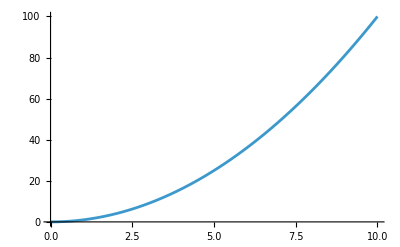
Out[108]:= -Graphics-

Out[109]:= Null

```mathematica
CLITools["Interface"]
```

```mathematica
CLITools["Interface", <|
("custom-command"|"c") :> (
Print["Running custom command"]
)
|>]
```

CLITools[Interface,{custom-command|c:>Print[Running custom command]}]

### Compatibility

#### Wolfram Language Version

12.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.